```mathematica
ClearAll[eom1,eom2,eom3,eom4,G,f3,g2,g1,eoma,f,G,g]
```

```mathematica
eom4[r_,j_]:=(3 f[r] (g[r]^2+r g'[r]-g[r]))/(g[r]^2 r^2)+(96 g[r]^3 f''''[r] f[r]^3 r^4-288 f[r]^2 g[r]^2 r^3 (r g[r] f'[r]+f[r] (r g'[r]-(4 g[r])/3)) f'''[r]-48 f[r]^3 g[r]^2 r^3 (r f'[r]+(2 f[r])/3) g'''[r]-212 (f''[r])^2 f[r]^2 g[r]^3 r^4-192 f[r] g[r] r^2 (g[r] f[r]^2 g''[r] r^2-(173 (f'[r])^2 g[r]^2 r^2)/48-(161 f[r] g[r] (r g'[r]-(30 g[r])/23) r f'[r])/48-(19 f[r]^2 ((g'[r])^2 r^2-(91 r g'[r] g[r])/57-(4 g[r]^2 (g[r]-1))/57))/8) f''[r]+312 f[r]^2 g[r] ((6 (f'[r])^2 g[r] r^2)/13+f[r] r (r g'[r]-(2 g[r])/3) f'[r]+(2 f[r]^2 (r g'[r]-(2 g[r])/13))/3) r^2 g''[r]-293 g[r]^3 (f'[r])^4 r^4-346 f[r] g[r]^2 r^3 (r g'[r]-(218 g[r])/173) (f'[r])^3-341 f[r]^2 g[r] r^2 ((g'[r])^2 r^2-(512 r g'[r] g[r])/341-(16 g[r]^2 (g[r]+1/4))/341) (f'[r])^2-336 f[r]^3 r (r^3 (g'[r])^3-(41 r^2 g[r] (g'[r])^2)/28-(g[r]^2 (g[r]+11/2) r g'[r])/21+(5 g[r]^3 (g[r]-1))/21) f'[r]-224 f[r]^4 (r^3 (g'[r])^3-(61 r^2 g[r] (g'[r])^2)/56-(13 g[r]^2 (g[r]-9/13) r g'[r])/14-(15 g[r]^3 (g[r]-1) (g[r]-19/15))/14)) j/(128 g[r]^5 f[r]^3 r^4);
eom3[r_,j_]:=(3 Sin[θ]^2 r (2 f''[r] g[r] r f[r]-f'[r] g'[r] r f[r]-(f'[r])^2 g[r] r-2 g'[r] f[r]^2+2 f'[r] g[r] f[r]))/(4 g[r]^2 f[r]^2)
+(3 Sin[θ]^2 j (-(g[r]^3 f[r]^3 f''''[r] r^4)/3+r^3 g[r]^2 ((5 f'[r] g[r] r)/6+f[r] (g'[r] r-g[r])) f[r]^2 f'''[r]+(r^3 f[r]^3 g[r]^2 (f'[r] r+14 f[r]) g'''[r])/6-(7 (f''[r])^2 g[r]^3 f[r]^2 r^4)/12+(2 r^2 g[r] (g''[r] g[r] f[r]^2 r^2-(9 (f'[r])^2 g[r]^2 r^2)/8-r g[r] (g'[r] r-(7 g[r])/2) f[r] f'[r]-(19 ((g'[r])^2 r^2-(56 g'[r] r g[r])/19-(8 g[r]^3)/19) f[r]^2)/8) f[r] f''[r])/3-(13 r^3 g[r] ((5 (f'[r])^2 g[r] r)/13+f[r] (g'[r] r-(34 g[r])/13) f'[r]+14 g'[r] f[r]^2) f[r]^2 g''[r])/12+(25 g[r]^3 (f'[r])^4 r^4)/48+(3 r^3 g[r]^2 (g'[r] r-(14 g[r])/3) f[r] (f'[r])^3)/8+(11 ((g'[r])^2 r^2-(160 g'[r] r g[r])/33-(16 g[r]^2 (g[r]+15/4))/33) r^2 g[r] f[r]^2 (f'[r])^2)/16+(7 (r^3 (g'[r])^3-(87 g[r] r^2 (g'[r])^2)/14-(2 r g[r]^2 (g[r]-5/2) g'[r])/7-2 g[r]^4+(10 g[r]^3)/7) r f[r]^3 f'[r])/6+(49 (r^3 (g'[r])^3-(15 g[r] r^2 (g'[r])^2)/196+(g[r]^2 r (g[r]-3) g'[r])/7+(5 (g[r]+23/5) g[r]^3 (g[r]-1))/49) f[r]^4)/3))/(8 g[r]^5 f[r]^4 r^2);
eom2[r_,j_]:=-(3 r (f'[r] g'[r] r f[r]-2 f''[r] g[r] r f[r]+(f'[r])^2 g[r] r+2 g'[r] f[r]^2-2 f'[r] g[r] f[r]))/(4 g[r]^2 f[r]^2)
+(-16 g[r]^3 f[r]^3 f''''[r] r^4+(40 r^4 f[r]^2 g[r]^3 f'[r]+48 f[r]^3 r^3 (g'[r] r-(5 g[r])/3) g[r]^2) f'''[r]+8 r^3 f[r]^3 g[r]^2 (f'[r] r+14 f[r]) g'''[r]-28 (f''[r])^2 g[r]^3 f[r]^2 r^4+32 f[r] r^2 ((g''[r] g[r] f[r]^2 r^2)-(9 (f'[r])^2 g[r]^2 r^2)/8-f[r] (g'[r] r-(11 g[r])/2) r g[r] f'[r]-(19 f[r]^2 ((g'[r])^2 r^2-(68 g'[r] r g[r])/19-(8 g[r]^2 (g[r]-2))/19))/8) g[r] f''[r]-52 f[r]^2 ((5 (f'[r])^2 g[r] r^2)/13+r f[r] (g'[r] r-(38 g[r])/13) f'[r]+14 f[r]^2 (g'[r] r-(8 g[r])/91)) r^2 g[r] g''[r]+25 g[r]^3 (f'[r])^4 r^4+18 f[r] (g'[r] r-(58 g[r])/9) r^3 g[r]^2 (f'[r])^3+33 f[r]^2 ((g'[r])^2 r^2-(64 g'[r] r g[r])/11-(16 g[r]^2 (g[r]-1/4))/33) r^2 g[r] (f'[r])^2+56 f[r]^3 (r^3 (g'[r])^3-(95 g[r] r^2 (g'[r])^2)/14-(2 (g[r]-13/2) r g[r]^2 g'[r])/7-2 g[r]^4+(18 g[r]^3)/7) r f'[r]+784 f[r]^4 (r^3 (g'[r])^3-(47 g[r] r^2 (g'[r])^2)/196+(g[r]^2 r (g[r]-3) g'[r])/7+(5 g[r]^3 (g[r]+3)(g[r]-1))/49)) j/(128 g[r]^5 f[r]^4 r^2);
eom1[r_,j_]:=(3 f'[r] r-3 f[r] (g[r]-1))/(r^2 f[r])+(-16 (3 f'[r] g[r] r+f[r] (r g'[r]+2 g[r])) f[r]^2 r^3 g[r]^2 f'''[r]+20 (f''[r])^2 g[r]^3 f[r]^2 r^4+24 f[r] ((19 (f'[r])^2 g[r]^2 r^2)/6+(7 f[r] r (r g'[r]-(6 g[r])/7) g[r] f'[r])/2+f[r]^2 ((g'[r])^2 r^2-r g'[r] g[r]+(4 g[r]^3)/3-4 g[r]^2)) r^2 g[r] f''[r]+8 (3 (f'[r])^2 g[r] r^2+r f[r] (r g'[r]+4 g[r]) f'[r]+4 f[r]^2 (r g'[r]+7 g[r])) f[r]^2 r^2 g[r] g''[r]-43 g[r]^3 (f'[r])^4 r^4-54 (r g'[r]-(22 g[r])/27) f[r] r^3 g[r]^2 (f'[r])^3-59 f[r]^2 r^2 ((g'[r])^2 r^2-(96 r g'[r] g[r])/59+(16 (g[r]-19/4) g[r]^2)/59) g[r] (f'[r])^2-16 (r^3 (g'[r])^3+(3 r^2 g[r] (g'[r])^2)/4+g[r]^2 r (g[r]-33/2) g'[r]-13 g[r]^4+9 g[r]^3) f[r]^3 r f'[r]-64 f[r]^4 (r^3 (g'[r])^3+(97 r^2 g[r] (g'[r])^2)/16+(9 g[r]^2 r (g[r]-1) g'[r])/4+(15 g[r]^5)/4-g[r]^4/2-(13 g[r]^3)/4)) j/(128 g[r]^4 f[r]^4 r^4);
(*Series ansatz*)g[r_]:=1/(1-2 M/r)+b2/r^2+b3/r^3+b4/r^4+b5/r^5;
f[r_]:=1-2 M/r+a2/r^2+a3/r^3+a4/r^4+a5/r^5;


(*Expand each equation in 1/r to a chosen order*)
ord=5;  (*increase if needed*)
ser1=Series[eom1[r,G],{r,Infinity,ord}]//Normal//Collect[#,1/r]&;
ser2=Series[eom4[r,G],{r,Infinity,ord+1}]//Normal//Collect[#,1/r]&;
ser3=Series[eom2[r,G],{r,Infinity,ord+1}]//Normal//Collect[#,1/r]&;

(*Extract coefficients and solve*)
coeffs1=CoefficientRules[ser1,1/r]/. {r->Infinity};  (*or use Coefficient[ser1,1/r,k]*)
coeffs2=CoefficientRules[ser2,1/r]/. {r->Infinity};
coeffs3=CoefficientRules[ser3,1/r]/. {r->Infinity};

(*Build the linear/nonlinear system from all coefficient equalities*)
sys=Thread[Values[coeffs1]==0]~Join~Thread[Values[coeffs2]==0]~Join~Thread[Values[coeffs3]==0];

(*Impose a1==1 to match f~1-1/r*)
sol=Solve[sys,{a2,a3,a4,b2,b3,b4,a5,b5,b6,a6},Reals]//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a2→0,a3→0,a4→-(G M^2)/12,b2→0,b3→0,b4→(G M^2)/3,a5→(77 G M^3)/460,b5→(271 G M^3)/1380}}

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

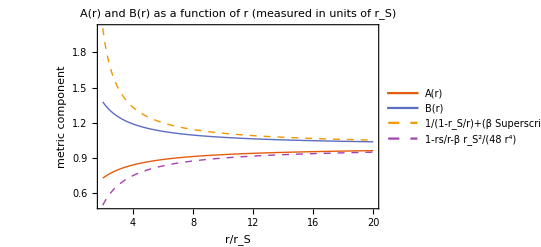

```mathematica
(*Example numerical integration skeleton once coefficients are known*)
ClearAll[f,g,F,G,k,R,r0,solNum]
R=5000;
r0=1;
G=1;
initF[r_]=1-1/r;
initG[r_]=1/(1-1/r);

ics={f[R]==initF[R],g[R]==initG[R],f'[R]==D[initF[r],r]/. r->R,g'[R]==D[initG[r],r]/. r->R,f''[R]==D[initF[r],r,r]/. r->R,g''[R]==D[initG[r],r,r]/. r->R};

solNum=NDSolve[{eom1[r,G]==0,eom2[r,G]==0,ics},{f,g},{r,r0,R},Method->{"IndexReduction"->Automatic}];
Plot[{Evaluate[g[r]]/.solNum,Evaluate[f[r]]/.solNum,1/(1-1/r)+G/(12 r^4),1-1/r-G/(48 r^4)},{r,2,20},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"r/r_S","metric component"},PlotLabel->"A(r) and B(r) as a function of r (measured in units of r_S)",PlotStyle->{{Thick},(*solid*){Thick},(*solid*){Dashed,Thick},(*dashed*){Dashed,Thick}        (*dashed*)},PlotLegends->Placed[{"A(r)","B(r)","1/(1-r_S/r)+(β  SuperscriptBox[SubscriptBox[r, S], 2])/(12 SuperscriptBox[r, 4])","1-rs/r-β r_S^2/(48 r^4)"},{0.5,0.7}]]
```

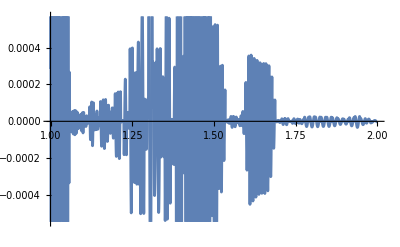

```mathematica
Plot[eom1[r,G]/.solNum,{r,1,2}]
```

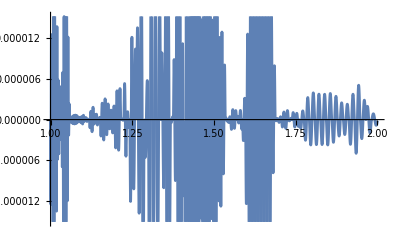

```mathematica
Plot[eom2[r,G]/.solNum,{r,1,2}]
```

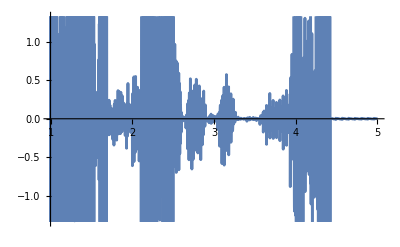

```mathematica
Plot[eom4[r,G]/.solNum,{r,1,5}]
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

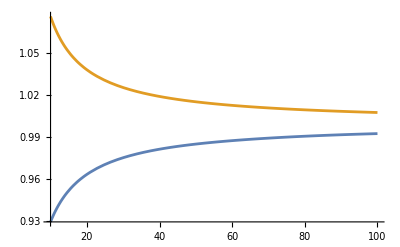

```mathematica
(*Example numerical integration skeleton once coefficients are known*)
ClearAll[f,g,F,G,k,R,solNum1]
R=5000;
G=1;
initF[r_]=1-1/r;
initG[r_]=1/(1-1/r);

ics={f[R]==initF[R],g[R]==initG[R],f'[R]==D[initF[r],r]/. r->R,g'[R]==D[initG[r],r]/. r->R,f''[R]==D[initF[r],r,r]/. r->R,g''[R]==D[initG[r],r,r]/. r->R};

solNum1=NDSolve[{eom2[r,G]==0,eom1[r,G]==0,ics},{f,g},{r,5,R},Method->{"IndexReduction"->Automatic}];
Plot[{Evaluate[g[r]]/.solNum1,Evaluate[f[r]]/.solNum1},{r,10,100},PlotRange->Full]
```

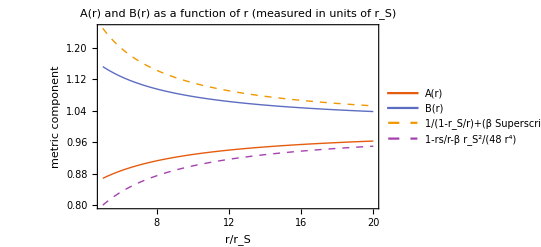

```mathematica
Plot[{Evaluate[g[r]]/.solNum1,Evaluate[f[r]]/.solNum1,1/(1-1/r)+G/(12 r^4),1-1/r-G/(48 r^4)},{r,5,20},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"r/r_S","metric component"},PlotLabel->"A(r) and B(r) as a function of r (measured in units of r_S)",PlotStyle->{{Thick},(*solid*){Thick},(*solid*){Dashed,Thick},(*dashed*){Dashed,Thick}        (*dashed*)},PlotLegends->Placed[{"A(r)","B(r)","1/(1-r_S/r)+(β  SuperscriptBox[SubscriptBox[r, S], 2])/(12 SuperscriptBox[r, 4])","1-rs/r-β r_S^2/(48 r^4)"},{0.8,0.8}]]
```

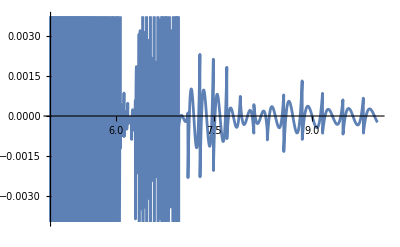

```mathematica
Plot[eom4[r,G]/.solNum1,{r,5,10}]
```

```mathematica
(*Example numerical integration skeleton once coefficients are known*)
ClearAll[initF,initG]
initF[r_]=Evaluate[f[r]]/.solNum1[[1]];
initG[r_]=Evaluate[g[r]]/.solNum1[[1]];
ClearAll[f,g,G,k,R,solNum]
R=10;
G=1;
ics={f[R]==initF[R],g[R]==initG[R],f'[R]==D[initF[r],r]/. r->R,g'[R]==D[initG[r],r]/. r->R,f''[R]==D[initF[r],r,r]/. r->R,g''[R]==D[initG[r],r,r]/. r->R};

solNum=NDSolve[{eom1[r,G]==0,eom4[r,G]==0,ics},{f,g},{r,1,R},Method->{"IndexReduction"->Automatic}];
Plot[{Evaluate[g[r]]/.solNum,Evaluate[f[r]]/.solNum},{r,2,10},PlotRange->Full]
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::ndsz: At r == 3.44637, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {2.00016} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Plot[eom4[r,G]/.solNum,{r,1,5}]
```

InterpolatingFunction::dmval: Input value {1.00008} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/((1.57127×10^108)^3) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((-7.97299×10^80)^5) is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
col=Collect[eom4[r,G],{g'''[r]},Simplify];
col
```

-((2 f[r]+3 r f'[r]) g^(3)[r])/(8 r g[r]^3)+1/(128 r^4 f[r]^3 g[r]^5)(-293 r^4 g[r]^3 f'[r]^4+2 r^3 f[r] g[r]^2 f'[r]^2 (-173 r f'[r] g'[r]+g[r] (218 f'[r]+346 r f''[r]))+4 f[r]^4 (-8 (17+12 r^2) g[r]^4+12 (5+8 r^2) g[r]^5-56 r^3 g'[r]^3+g[r]^3 (76+(52 r+96 r^3) g'[r])-4 r g[r]^2 (9 g'[r]+2 r g''[r])+r^2 g[r] g'[r] (61 g'[r]+52 r g''[r]))+r^2 f[r]^2 g[r] (16 g[r]^3 f'[r]^2-341 r^2 f'[r]^2 g'[r]^2+4 r g[r] f'[r] (161 r g'[r] f''[r]+4 f'[r] (32 g'[r]+9 r g''[r]))+4 g[r]^2 (f'[r]^2-53 r^2 f''[r]^2-6 r f'[r] (35 f''[r]+12 r f^(3)[r])))+4 r f[r]^3 (-84 r^3 f'[r] g'[r]^3-4 g[r]^4 (5 f'[r]+2 r f''[r])+3 r^2 g[r] g'[r] (38 r g'[r] f''[r]+f'[r] (41 g'[r]+26 r g''[r]))-2 r g[r]^2 (f'[r] (-11 g'[r]+26 r g''[r])+r (24 r f''[r] g''[r]+g'[r] (91 f''[r]+36 r f^(3)[r])))+4 g[r]^3 (f'[r] (5+r g'[r])+2 r (f''[r]+3 r (4 f^(3)[r]+r f^(4)[r])))))

```mathematica
Solve[eom2[r,G]==0,g'[r]]
```

{{g'[r]→(g[r] (2 f[r] f'[r]-r f'[r]^2+2 r f[r] f''[r]))/(f[r] (2 f[r]+r f'[r]))}}

NDSolve::ndsz: At r == 1.06906, step size is effectively zero; singularity or stiff system suspected.

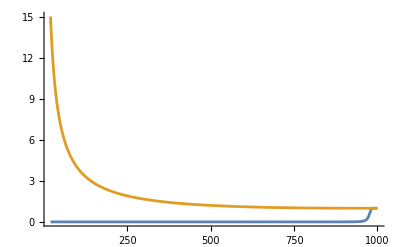

```mathematica
ClearAll[g1,g3,g2,eoma]
g1[r_]:=(g[r] (2 f[r] f'[r]-r f'[r]^2+2 r f[r] f''[r]))/(f[r] (2 f[r]+r f'[r]));
g2[r_]:=D[g1[z],z]/.z->r//Simplify;
g3[r_]:=D[g2[z],z]/.z->r//Simplify;
eoma = eom4[r,G]/. Derivative[3][g][r]->g3[r]/.g''[r]->g2[r]/.g'[r]->g1[r]//Simplify;
(*Numerical evaluation of the two reduced equations*)
ClearAll[f,g,F,G,k,R,r0,solNum,initF,initG]
R=1000;
r0=1;
G=1;
initF[r_]=1-(1/r);
initG[r_]=1/(1-(1/r));

ics={f[R]==initF[R],g[R]==initG[R],f'[R]==D[initF[r],r]/. r->R,g'[R]==D[initG[r],r]/. r->R,f''[R]==D[initF[r],r,r]/.r->R,g''[R]==D[initG[r],r,r]/. r->R};

solNum=NDSolve[{eoma==0,eom1[r,G]==0,ics},{f,g},{r,r0,R},Method->{"IndexReduction"->Automatic}];
Plot[{Evaluate[g[r]]/.solNum,Evaluate[f[r]]/.solNum},{r,20,1000},PlotRange->Full]
```